```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poincare/Dropbox/Documentos/DMKM/01 Lyon/Courseware/Op/04

```mathematica
err2=Flatten[Import["err2nu2.mat"]];
err2=Table[{N[2^(i-10)],err2[[i]]*100},{i,20}];
```

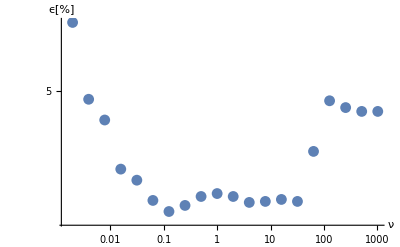

```mathematica
ex1=ListLogLogPlot[err2,AxesLabel->{"ν","ϵ[%]"}](*1000 training set*)
```

```mathematica
Export["ex1.eps",ex1]
```

ex1.eps

```mathematica
err2
```

{{0.00195313,6.06776},{0.00390625,4.88706},{0.0078125,4.60986},{0.015625,4.01437},{0.03125,3.89117},{0.0625,3.67556},{0.125,3.56263},{0.25,3.62423},{0.5,3.71663},{1.,3.74743},{2.,3.71663},{4.,3.65503},{8.,3.6653},{16.,3.68583},{32.,3.6653},{64.,4.21971},{128.,4.86653},{256.,4.77413},{512.,4.72279},{1024.,4.72279}}

```mathematica
2^10
```

1024